## Week 8 - Lecture 6: Central Limit Theorem

Resources  --  Video  &&  Notes 8f

#### Generating random walk uniformly from interval [-1,1]

```mathematica
a={0};
Do[
AppendTo[a, a[[n-1]]+1-2RandomReal[]],
{n,2,500}];
ListPlot[a, Joined->True]
```

-Graphics-

#### Variance - Analytical vs Numerical

σ^2 = ∫x^2f(x)dx - (∫xf(x)dx)^2

Integrating with mean=0 and f(x)=1/(b-a) under the limits (-1,1), we get 
Variance=x^3/6 = 1/3

This variance is for 1 random variable. For N trials of the same random variable,
Variance = N/3 (Central Limit Theorem)

```mathematica
data = Table[
variance=Mean[Table[
Total[Table[1-2RandomReal[], {n}]], (* Calculate m *)
{10000}]^2 // N]; (* Calculate m^2 many times & compute <m^2> *)
{n, variance}, {n,100,1000,100}]; (* 'n' is the number of steps N *)
```

```mathematica
Show[ListPlot[data, PlotStyle->Red], Plot[x/3, {x,0,1500}]]
```

-Graphics-

#### Probability Distribution - Analytical vs Numerical

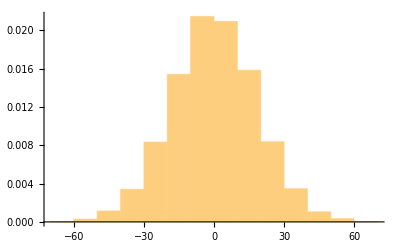

```mathematica
nMax = 1000; (* Fixed number of steps *)
binsize = 10;
histdata = Histogram[Table[
Total[Table[1-2RandomReal[], {nMax}]], (* Compute m *)
{10000}], {binsize}, "PDF"] (* Generate large no. of m's, and normalize them to get PDF*)
```

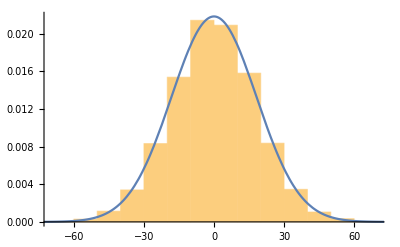

```mathematica
unbiasedsoln[x_, N_] = Exp[-x^2/(2N/3)]/Sqrt[2π N/3];
Show[histdata, 
Plot[unbiasedsoln[x,nMax], {x, -5√nMax, 5 √nMax}]]
```

### Random Walk using Standard Normal Distribution

```mathematica
a={0};
Do[
AppendTo[a, a[[n-1]]+RandomVariate[NormalDistribution[]]],
{n,2,500}];
ListPlot[a, Joined->True]
```

-Graphics-

Variance

```mathematica
data = Table[
variance=Mean[Table[
Total[Table[RandomVariate[NormalDistribution[]], {n}]], (* Calculate m *)
{10000}]^2 // N]; (* Calculate m^2 many times & compute <m^2> *)
{n, variance}, {n,100,1000,100}]; (* 'n' is the number of steps N *)
Show[ListPlot[data, PlotStyle->Red], Plot[x, {x,0,1500}]] (*Analytical Var=N*1=N*)
```

-Graphics-

We see that it agrees with CLT

Probability Distribution

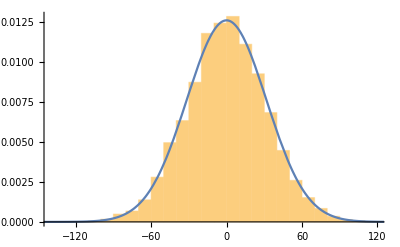

```mathematica
nMax = 1000; (* Fixed number of steps *)
binsize = 10;
histdata = Histogram[Table[
Total[Table[RandomVariate[NormalDistribution[]], {nMax}]], (* Compute m *)
{10000}], {binsize}, "PDF"];
unbiasedsoln[x_, N_] = Exp[-x^2/(2N)]/Sqrt[2π N];
Show[histdata, 
Plot[unbiasedsoln[x,nMax], {x, -5√nMax, 5 √nMax}]]
```

Similarly we can do the same for any distribution and see this Gaussian behavior, thanks to CLT.

### Why is the law of diffusive scaling so general?

Check page 6 for an general argument using vectors in any N-dimensional space.
Finally we see that the if you take N steps, you have only moved ∝ √N only. (In our above examples, we had our a=1)